```mathematica
α=0.0005499651141443689;
```

```mathematica
T=491.535;
```

```mathematica
wo=Sqrt[(2*Pi/T)^2+(α/2)^2];
```

```mathematica
τ=2*0.05*(1-0.058772338)*6.863155982898358^(-11)*((1.5*0.0383)/0.0422^2);
```

```mathematica
(*El 2 de aquí abajo es mb, se podría cambiar*)
```

```mathematica
I1=2*0.0383*(0.05^2+(2/5)*0.00955^2)+(1/3)*2*0.05^2;
```

```mathematica
w1=2*Pi/T;
```

```mathematica
θ[t_]:=(τ/(I1*wo^2))*(1-E^(-(α*t)/2)*(Cos[w1*t]+(α/(2*w1))*Sin[w1*t]))
```

```mathematica
p=Plot[2*θ[t]*318.54,{t,-100,8000},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{-100,4000},{-0.2,8}},Frame->True,FrameLabel->{Style["t / s",Bold,16],Style[" 2Lθ / rad cm",16,Bold]},PlotLegends->{"Curva 2Lθ (t)"}];
```

```mathematica
dataTHETAmin={{0,0},{1*T,0.4},{2*T,0.9},{3*T,1.2},{4*T,1.4},{5*T,1.9},{6*T,2.1},{7*T,2.3}};
```

```mathematica
dataTHETAmax={{0.5*T,7.9},{1.5*T,7.4},{2.5*T,7.1},{3.5*T,6.5},{4.5*T,6.2},{5.5*T,6},{6.5*T,5.6},{7.5*T,5.4}};
```

```mathematica
plotdatamin=ListPlot[dataTHETAmin,PlotStyle->{Black,Thickness[0.003]},PlotLegends -> {"Datos experimentales"}];
```

```mathematica
plotdatamax=ListPlot[dataTHETAmax,PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
dataerrmin=ErrorListPlot[{{{0,0},ErrorBar[0,0.102833734]},{{1*T,0.4},ErrorBar[4.606,0.102833734]},{{2*T,0.9},ErrorBar[9.212,0.102833734]},{{3*T,1.2},ErrorBar[13.819,0.102833734]},{{4*T,1.4},ErrorBar[18.425,0.102833734]},{{5*T,1.9},ErrorBar[23.032,0.102833734]},{{6*T,2.1},ErrorBar[27.638,0.102833734]},{{7*T,2.3},ErrorBar[32.244,0.102833734]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.002]}];
```

```mathematica
dataerrmax=ErrorListPlot[{{{0.5*T,7.9},ErrorBar[2.303,0.102833734]},{{1.5*T,7.4},ErrorBar[6.909,0.102833734]},{{2.5*T,7.1},ErrorBar[11.516,0.102833734]},{{3.5*T,6.5},ErrorBar[16.122,0.102833734]},{{4.5*T,6.2},ErrorBar[20.728,0.102833734]},{{5.5*T,6},ErrorBar[25.335,0.102833734]},{{6.5*T,5.6},ErrorBar[29.941,0.102833734]},{{7.5*T,5.4},ErrorBar[34.548,0.102833734]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.002]}];
```

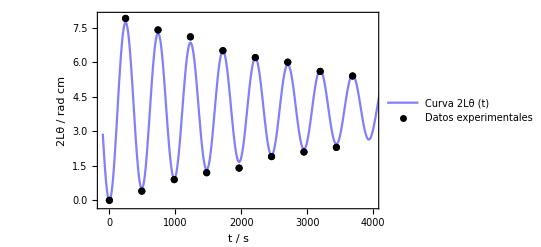

```mathematica
Show[p,plotdatamin,plotdatamax,dataerrmin,dataerrmax]
```